# Setup

```mathematica
Get["C:\\Users\\Miguel\\Github\\libs\\QMB\\Kernel\\init.m"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
LaunchKernels[12];
```

```mathematica
Names["QMB`*"]
```

{AnalyticalNumberVarianceGOE,AnalyticalNumberVarianceGUE,AnalyticalNumberVariancePoisson,ARQMHamiltonian,BlochVector,BoseHubbardHamiltonian,BoseHubbardHilbertSpaceDimension,BosonEscapeKrausOperators,BosonicPartialTrace,Braket,ClassicalMapeo,ClassicalStep,ClassicalToDisk,ClassicalToSphere,COEAsymptoticSigma2,COESFFAnalytical,coherentstate,CommutationQ,CompileLevelCounter,CompileSFF,ComplexSpacingRatios,ComplexToPolar,ComputeSigma2Sliding,Concurrence,DensityMatrix,Dyad,EigenvectorQ,EmpiricalKLDivergence,EnsembleSFF,EnsembleSigma2,EvaluateSpectrumSigma2,FixCkForStateEvoultion,Floq,Floqb,Floqbn,Floqn,Floqsym,FluctuationPowerSpectrum,FockBasis,FockBasisIndex,FockBasisStateAsColumnVector,FuzzyMeasurement,FuzzyMeasurementChannel,GenerateCOEEnsemble,generateCoherentStateCompiler,GenerateGinibreMatrix,GenerateQKTEnsemble,generateSpinOperators,GetFluctuations,GetQKTParityEigensystem,GetQKTParitySpectra,HaarRandomState,HilbertSpaceDim,InitializationBosonicPartialTrace,InitializeVariables,IntWignerCOE,IPR,KetInComputationalBasisFromVector,KineticTermBoseHubbardHamiltonian,KLDivergence,KroneckerVectorProduct,kthOrderSpacings,LengthSpectrum,LevelSpacingDistribution,MatrixCommutator,MatrixPartialTrace,MatrixPartialTraceFromPureState,MeanLevelSpacingRatio,MutuallyCommutingSetQ,NNSpacings,NormalizedSpacingRatios,NumberVariance,ParitySectorIndices,PartialTranspose,Pauli,PoolSpacingRatios,PoolSpacings,PotentialTermBoseHubbardHamiltonian,PrCOE,PrCUE,PrPoisson,Purity,QuantumTexture,Qubit,QubitStateFromBlochVector,RandomChainProductState,RandomCOESpectrum,RandomQubitState,RandomSU2Parameters,RandomSU2Rotation,RatiosDistribution,RatiosDistributionPoisson,RenyiEntropy,Reshuffle,SingleSFF,SingleSpectrumSigma2,SortFockBasis,SpacingRatios,SpectralFormFactor,SpectralFormFactorRMT,StateEvolution,SU2Rotation,SU2RotationParameters,SuperoperatorFromU,SwapMatrix,SymmetricSubspace,Tag,TimeAveragedSFF,Unfold,UnfoldLinear,ValidateUnfolding,VectorFromKetInComputationalBasis,WeylMatrix,WignerCOE,ω}

# Choi-State Method Validation: Brute-Force vs Transfer-Tensor

Purpose: numerically test whether the proposed transfer-tensor Choi
construction (Method 2) reproduces the brute-force SpectralUnitary 
construction (Method 1, identical to spin_choi_comparison_fixed.m's 
Branch B) to within floating-point tolerance. No reduced-state (edge-
spin) observables are computed here -- rhoAB plays no role in either 
Choi construction, by design. Both methods are evaluated on the SAME
{Eval,Evec} diagonalization and the SAME rhoChain, over the SAME tlist,
so results are directly comparable index-by-index without any 
re-alignment.

## Definitions -- Hamiltonian, Couplings, Environment State

```mathematica
(* ================================================================ *)
(* BLOCK 0 -- Kernel setup                                          *)
(* ================================================================ *)
$CompileTarget = "C";
```

```mathematica
(* ================================================================ *)
(* BLOCK 1 -- Pauli operators                                        *)
(* ================================================================ *)
σx  = N[PauliMatrix[1]];
σy  = N[PauliMatrix[2]];
σz  = N[PauliMatrix[3]];
σp  = σx + I*σy;
σm  = σx - I*σy;
id2 = N[IdentityMatrix[2]];
```

```mathematica
(* ================================================================ *)
(* BLOCK 2 -- Hamiltonian embedding functions, [Q1, Chain, Q2] layout *)
(* ================================================================ *)
Clear[SparseId,EmbedSpinA,EmbedSpinB,EmbedChain,EmbedChainSite];
SparseId[n_] := SparseArray[Band[{1, 1}] -> 1., {n, n}];
EmbedSpinA[op_, L_] :=
  KroneckerProduct[op, SparseId[2^L], SparseId[2]];
EmbedSpinB[op_, L_] :=
  KroneckerProduct[SparseId[2], SparseId[2^L], op];
EmbedChain[Ha_, L_] :=
  KroneckerProduct[SparseId[2], Ha, SparseId[2]];
EmbedChainSite[op_, k_, L_] :=
  KroneckerProduct[SparseId[2^(k - 1)], op, SparseId[2^(L - k)]];
```

```mathematica
(* ================================================================ *)
(* BLOCK 3 -- Boundary coupling constructors                        *)
(* A-chain couples spin A to the FIRST chain site.                  *)
(* B-chain couples spin B to the LAST  chain site.                  *)
(* ================================================================ *)
Clear[BuildCouplingAChain, BuildCouplingBChain];

BuildCouplingAChain[couplingTerms_, L_] := Sum[
  term[[1]] * KroneckerProduct[
    term[[2]],
    KroneckerProduct[term[[3]], SparseId[2^(L - 1)]],
    SparseId[2]
  ],
  {term, couplingTerms}
];

BuildCouplingBChain[couplingTerms_, L_] := Sum[
  term[[1]] * KroneckerProduct[
    SparseId[2],
    KroneckerProduct[SparseId[2^(L - 1)], term[[2]]],
    term[[3]]
  ],
  {term, couplingTerms}
];
```

```mathematica
(* ================================================================ *)
(* BLOCK 4 -- Full Hamiltonian assembler and diagonalization        *)
(* ================================================================ *)
Clear[BuildFullHamiltonian,DiagonalizeH];
BuildFullHamiltonian[HAlocal_, Ha_, HBlocal_, couplingA_, couplingB_, L_] :=
  EmbedSpinA[HAlocal, L] +
  EmbedChain[Ha, L]        +
  EmbedSpinB[HBlocal, L]  +
  BuildCouplingAChain[couplingA, L] +
  BuildCouplingBChain[couplingB, L];

DiagonalizeH[HT_] := Transpose[Sort[Transpose[Eigensystem[Normal[N[HT]]]]]];
```

```mathematica
(* ================================================================ *)
(* BLOCK 5 -- Thermal state of the chain at inverse temperature beta.*)
(*   beta = 0        -> maximally mixed (infinite temperature)       *)
(*   beta = Infinity -> ground-state projector (zero temperature)    *)
(*   otherwise       -> Gibbs state exp(-beta H) / Z                 *)
(* ================================================================ *)
Clear[ThermalChainState];
ThermalChainState[Ha_, beta_] := Module[
  {vals, vecs, weights, Z},
  Which[
    beta == 0.,
      N[IdentityMatrix[Length[Ha]]] / Length[Ha],
    beta === Infinity,
      {vals, vecs} = Transpose[Sort[Transpose[Eigensystem[N[Ha]]]]];
      Outer[Times, vecs[[1]], Conjugate[vecs[[1]]]],
    True,
      {vals, vecs} = Transpose[Sort[Transpose[Eigensystem[N[Ha]]]]];
      weights = Exp[-beta * (vals - Min[vals])];
      Z = Total[weights];
      ConjugateTranspose[vecs] . DiagonalMatrix[N[weights / Z]] . vecs
  ]
];
```

## Definitions -- Choi Machinery Shared by Both Methods

```mathematica
(* ================================================================ *)
(* Packing utility.                                                  *)
(* ================================================================ *)
Needs["Developer`"];
ClearAll[PackedC];
PackedC[x_] := Developer`ToPackedArray[N[x]];
```

```mathematica
(* ================================================================ *)
(* Choi-state observables, derived from the dS^2 x dS^2 Choi matrix. *)
(* Identical for both methods -- operates only on the resulting     *)
(* numerical matrix, with no knowledge of how it was constructed.   *)
(* ================================================================ *)
ClearAll[ChoiPurity, ChoiVNEntropy, ChoiEVals, ChoiAllObs];

ChoiPurity[choiMat_] := Chop@Re@Tr[choiMat . choiMat];

ChoiVNEntropy[choiMat_] :=
  Module[{ev = Select[Re[Eigenvalues[N[choiMat]]], # > 1.*^-14 &]},
    ev = ev / Total[ev];
    Chop@(-ev . Log[ev])];

ChoiEVals[choiMat_] :=
  Sort[Select[Re[Eigenvalues[N[choiMat]]], # > 1.*^-14 &], Greater];

ChoiAllObs[choiMat_] :=
  Module[{ev = Sort[Select[Re[Eigenvalues[N[choiMat]]], # > 1.*^-14 &], Greater],
          evNorm},
    evNorm = ev / Total[ev];
    <|"Purity"      -> Chop@Re@Tr[choiMat . choiMat],
      "VNEntropy"   -> Chop@(-evNorm . Log[evNorm]),
      "Eigenvalues" -> ev,
      "Rank"        -> Length[ev]|>];
```

```mathematica
(* ================================================================ *)
(* Time-series driver. Takes ANY Function[t, choiMat(t)] closure --  *)
(* both methods below produce one with this exact interface, so this*)
(* driver is reused verbatim for Method 1 and Method 2.              *)
(* ================================================================ *)
ClearAll[ChoiSeries];
Options[ChoiSeries] = {"Observables" -> "All", "Parallel" -> True};

ChoiSeries[choiFn_Function, tlist_List, OptionsPattern[]] :=
  Module[{obsOpt = OptionValue["Observables"],
          parOpt = TrueQ[OptionValue["Parallel"]],
          stepFn},
    stepFn = Function[{t},
      Module[{choiMat = choiFn[t], obsResult},
        obsResult = Switch[obsOpt,
          "Purity",
            <|"Purity" -> ChoiPurity[choiMat]|>,
          "Entropy",
            Module[{ev = Sort[Select[Re[Eigenvalues[N[choiMat]]],
                                    # > 1.*^-14 &], Greater]},
              ev = ev / Total[ev];
              <|"Purity"    -> Chop@Re@Tr[choiMat . choiMat],
                "VNEntropy" -> Chop@(-ev . Log[ev])|>],
          _,
            ChoiAllObs[choiMat]];
        Join[<|"Time" -> t|>, obsResult]]];
    If[parOpt,
      ParallelMap[stepFn, tlist,
        Method -> "CoarsestGrained",
        DistributedContexts -> None],
      Map[stepFn, tlist]]];
```

```mathematica
(* ================================================================ *)
(* Result extraction utilities.                                      *)
(* ================================================================ *)
ClearAll[ExtractTS, ExtractEVals];

ExtractTS[res_List, key_String] :=
  {#["Time"], #[key]} & /@ res;

ExtractEVals[res_List, nKeep_Integer] :=
  Table[
    {#["Time"],
     If[Length[#["Eigenvalues"]] >= k, #["Eigenvalues"][[k]], 0.]} & /@ res,
    {k, 1, nKeep}];
```

## Method 1 -- Brute-Force Choi Construction (unoptimized, ground truth)

Identical to spin_choi_comparison_fixed.m's Branch B / choi_test_flat.m.
SpectralUnitary rebuilds the full D_total x D_total unitary at every t,
then evolves the doubled R x S x E state explicitly. This branch is 
NOT modified -- it is the reference result against which Method 2 is 
checked.

```mathematica
(* ================================================================ *)
(* Eigenvector column permutation: [Q1,Chain,Q2] -> [Q1,Q2,Chain]    *)
(* = S x E, where S = Q1 x Q2 (dS=4) and E = Chain (dE = 2^L).      *)
(* ================================================================ *)
Clear[PermuteEvecsToSE];
PermuteEvecsToSE[Evec_, L_] := Module[
  {dC = 2^L},
  PackedC@Table[
    Flatten[Transpose[ArrayReshape[Evec[[alpha]], {2, dC, 2}], {1, 3, 2}]],
    {alpha, 1, Length[Evec]}
  ]
];
```

```mathematica
(* ================================================================ *)
(* Spectral unitary: Function[t, U(t)], rebuilt fully at each call. *)
(* ================================================================ *)
ClearAll[SpectralUnitary];
SpectralUnitary[allvecs_, allvals_] :=
  Module[{Pmat  = PackedC@Transpose[allvecs],
          Pinv  = PackedC@Conjugate[allvecs]},
    Function[{t},
      With[{ph = PackedC@Exp[-I allvals t]},
        PackedC@(Transpose[Transpose[Pmat]*ph] . Pinv)]]];
```

```mathematica
(* ================================================================ *)
(* Maximally entangled reference-system projector |Phi+><Phi+|.    *)
(* ================================================================ *)
ClearAll[MakePhiProjector];
MakePhiProjector[dS_Integer?Positive] :=
  Module[{phi = PackedC@(Flatten[IdentityMatrix[dS]]/Sqrt[dS])},
    PackedC@Dyad[phi]];
```

```mathematica
(* ================================================================ *)
(* Choi channel builder: choiMat(t) = Tr_E[(I_R x U(t)) (|Phi+><Phi+| x rhoE) (I_R x U(t))^dagger] *)
(* "rhoE" -> dE x dE environment initial density matrix.            *)
(* ================================================================ *)
ClearAll[ChoiChannelF];
Options[ChoiChannelF] = {"rhoE" -> None};

ChoiChannelF[dS_Integer?Positive, dE_Integer?Positive,
             unitaryF_Function, opts:OptionsPattern[]] :=
  Module[{rhoEval = OptionValue["rhoE"],
          projPhi, idRef},
    If[rhoEval === None,
      Message[ChoiChannelF::noenv]; Return[$Failed]];
    rhoEval = PackedC@rhoEval;
    projPhi = MakePhiProjector[dS];
    idRef   = IdentityMatrix[dS, SparseArray];
    Function[{t},
      Module[{Ut = unitaryF[t], URt, OmegaMat, fullMat},
        URt      = KroneckerProduct[idRef, Ut];
        OmegaMat = KroneckerProduct[projPhi, rhoEval];
        fullMat  = URt . OmegaMat . ConjugateTranspose[URt];
        PackedC@Chop@MatrixPartialTrace[fullMat, 3, {dS, dS, dE}]]]];

ChoiChannelF::noenv = "Provide \"rhoE\" -> (dE x dE matrix).";
```

## Method 2 -- Transfer-Tensor Choi Construction (proposed optimization)

Uses the Choi-Jamiolkowski operator-basis identity
  J(eps) = Sum_ij |i><j| (x) eps(|i><j|)
instead of the teleportation (doubled-space) construction. eps(|i><j|)
is computed with the SAME transfer-tensor / K-matrix machinery already
validated for the reduced edge-spin propagation, fed with the input
operator |i><j| (x) rhoChain instead of rhoAB (x) rhoChain. Works 
directly in the native [Q1,Chain,Q2] layout -- no PermuteEvecsToSE, 
no SpectralUnitary, no doubled-space Kronecker products, no generic 
MatrixPartialTrace call. Hermiticity (eps(|i><j|) = eps(|j><i|)^dagger)
is used to compute only the 10 of 16 (i,j) blocks with i<=j; the 
remaining 6 are filled by conjugate transpose -- exact, not approximate.

```mathematica
(* ================================================================ *)
(* Transfer tensor builder, [Q1,Chain,Q2] eigenvectors.              *)
(* T[[q1+1,q2+1,q1p+1,q2p+1]] is a D_total x D_total matrix, OUTPUT- *)
(* basis indexed. Depends only on Evec -- shared by every (i,j) input*)
(* pair below, built once.                                           *)
(* ================================================================ *)
Clear[BuildTransferTensors];
BuildTransferTensors[U_, L_] := Module[
  {dC, idxFull, getCols},
  dC       = 2^L;
  idxFull  = Compile[{{q1,_Integer},{c,_Integer},{q2,_Integer},{dC,_Integer}},
               q1*(2*dC) + c*2 + q2 + 1,
               CompilationTarget -> $CompileTarget];
  getCols[q1_, q2_] := Table[idxFull[q1, c, q2, dC], {c, 0, dC - 1}];
  ParallelTable[
    Conjugate[U[[All, getCols[q1, q2]]]] . Transpose[U[[All, getCols[q1p, q2p]]]],
    {q1, 0, 1}, {q2, 0, 1}, {q1p, 0, 1}, {q2p, 0, 1}
  ]
];
```

```mathematica
(* ================================================================ *)
(* K-matrix builder: absorbs a Dtot x Dtot energy-basis operator into*)
(* the transfer tensor. Generic in its first argument -- reused here *)
(* with the per-(i,j) input projection M_ij in place of the full *)
(* joint-state projection used for the reduced edge-spin state.      *)
(* ================================================================ *)
Clear[BuildKMatrix];
BuildKMatrix[ρE_, T_] := ArrayReshape[
  Table[
    Flatten[ρE * T[[q1+1, q2+1, q1p+1, q2p+1]]],
    {q1, 0, 1}, {q2, 0, 1}, {q1p, 0, 1}, {q2p, 0, 1}
  ],
  {4, 4, Length[ρE]^2}
];
```

```mathematica
(* ================================================================ *)
(* Energy difference vector (shared with the reduced-state pipeline; *)
(* depends only on Eval).                                            *)
(* ================================================================ *)
Clear[BuildEnergyDiffs];
BuildEnergyDiffs[E_] := Flatten[Outer[Subtract, E, E]];
```

```mathematica
(* ================================================================ *)
(* Per-step contraction: Kmat . exp(-i dE t) -> 4x4 output block.    *)
(* ================================================================ *)
Clear[ComputeRhoAB];
ComputeRhoAB[Kmat_, dEflat_, t_?NumericQ] :=
  Kmat . Exp[(-I) * dEflat * t];
```

```mathematica
(* ================================================================ *)
(* Edge-basis column extractor: returns {U1,U2,U3,U4}, each a       *)
(* D_total x dC matrix selecting the columns of Evec with the edge   *)
(* spins fixed at INPUT basis state s (s=1..4 <-> (q1,q2) with q1 the*)
(* high bit, q2 the low bit -- matches PermuteEvecsToSE's S-ordering*)
(* by construction, and matches BuildTransferTensors' getCols).      *)
(* ================================================================ *)
Clear[EdgeColumnBlocks];
EdgeColumnBlocks[Evec_, L_] := Module[
  {dC = 2^L, idxFull, getCols},
  idxFull = Compile[{{q1,_Integer},{c,_Integer},{q2,_Integer},{dC,_Integer}},
               q1*(2*dC) + c*2 + q2 + 1,
               CompilationTarget -> $CompileTarget];
  getCols[q1_, q2_] := Table[idxFull[q1, c, q2, dC], {c, 0, dC - 1}];
  Table[
    Evec[[All, getCols[Quotient[s - 1, 2], Mod[s - 1, 2]]]],
    {s, 1, 4}
  ]
];
```

```mathematica
(* ================================================================ *)
(* Per-(i,j) K-matrices. M_ij = Conj[U_i] . rhoChain . Transpose[U_j]*)
(* is the energy-basis projection of |i><j| (x) rhoChain, computed   *)
(* directly without ever forming the dense D_total x D_total operator*)
(* |i><j| (x) rhoChain. Only i<=j (10 of 16 pairs) are built; the    *)
(* rest are recovered by conjugate transpose at evaluation time.     *)
(* ================================================================ *)
Clear[BuildChoiKMatricesFast];
BuildChoiKMatricesFast[Evec_, L_, rhoChain_, T_] := Module[
  {Ucols},
  Ucols = EdgeColumnBlocks[Evec, L];
  Table[
    If[i <= j,
      BuildKMatrix[Conjugate[Ucols[[i]]] . rhoChain . Transpose[Ucols[[j]]], T],
      Null
    ],
    {i, 1, 4}, {j, 1, 4}
  ]
];
```

```mathematica
(* ================================================================ *)
(* Choi matrix assembly at time t. Computes the 10 upper-triangle    *)
(* (i<=j) output blocks via ComputeRhoAB, fills the lower triangle by*)
(* conjugate transpose (exact, not approximate), and stacks all 16   *)
(* 4x4 blocks into the dS^2 x dS^2 Choi matrix.                      *)
(* ================================================================ *)
Clear[ComputeChoiMatrixFast];
ComputeChoiMatrixFast[Kmat_, dEflat_, t_?NumericQ, dS_Integer] := Module[
  {upper, blocks},
  upper = Table[
    If[i <= j, Chop[ComputeRhoAB[Kmat[[i, j]], dEflat, t]], Null],
    {i, 1, 4}, {j, 1, 4}
  ];
  blocks = Table[
    If[i <= j, upper[[i, j]], ConjugateTranspose[upper[[j, i]]]],
    {i, 1, 4}, {j, 1, 4}
  ];
  PackedC[ArrayFlatten[blocks] / dS]
];
```

```mathematica
(* ================================================================ *)
(* Fast Choi channel builder: returns Function[t, choiMat(t)], same *)
(* interface as ChoiChannelF, so ChoiSeries works unchanged on both. *)
(* ================================================================ *)
Clear[BuildChoiFnFast];
BuildChoiFnFast[KmatIn_, dEflatIn_, dSIn_Integer] := Module[
  {Kmat = KmatIn, dEflat = dEflatIn, dS = dSIn},
  Function[{t}, ComputeChoiMatrixFast[Kmat, dEflat, t, dS]]
];
```

## Model Specification -- FIXED Parameters (No Sweeps, Validation Size)

```mathematica
(* --- System size (kept small: brute-force method must finish) --- *)
L =6;
```

```mathematica
(* --- Edge-spin local fields and boundary couplings --- *)
{Δa, Δb, λa, λb} = {1., 1., 1., 1.};
HAlocal   = Δa * σz;
HBlocal   = Δb * σz;
couplingA = {{λa, σp, σm}, {λa, σm, σp}};
couplingB = {{λb, σp, σm}, {λb, σm, σp}};
```

```mathematica
(* --- Chain model: XXZwLocalDefectHamiltonian[Jxy,Jz,w,ed,L,d] --- *)
(* Defect terms off (w=ed=0) -> clean XXZ chain. Jz = delta, FIXED. *)
{Jxy, w, ed} = {1., 0, 0};
delta = 1.0;
```

```mathematica
(* --- Bipartition dimensions for the Choi construction --- *)
dS = 4;        (* S = Q1 x Q2, the two edge spins *)
dE = 2^L;      (* E = Chain *)
```

```mathematica
(* --- Fixed inverse temperature for the chain's initial state --- *)
(* A generic finite beta is used deliberately (not 0 or Infinity), *)
(* since those two limits are numerically degenerate special cases.*)
beta = 100.;
```

```mathematica
(* --- Time grid --- *)
tMax = 50.;
dt   = 0.1;
tlist = Range[0., tMax, dt];
```

```mathematica
Print["Fixed parameters:"];
Print["  L = ", L, "   delta = ", delta, "   beta = ", beta];
Print["  {Deltaa, Deltab, lambda_a, lambda_b} = ", {Δa, Δb, λa, λb}];
Print["  {Jxy, w, ed} = ", {Jxy, w, ed}];
Print["  dS = ", dS, "   dE = ", dE, "   D_total = ", dS*dE];
Print["  tMax = ", tMax, "   dt = ", dt, "   steps = ", Length[tlist]];
```

Fixed parameters:

L = 6   delta = 1.   beta = 100.

{Deltaa, Deltab, lambda_a, lambda_b} = {1.,1.,1.,1.}

{Jxy, w, ed} = {1.,0,0}

dS = 4   dE = 64   D_total = 256

tMax = 50.   dt = 0.1   steps = 501

## Build and Diagonalize the Full Hamiltonian (shared by both methods)

```mathematica
Ha = XXZwLocalDefectHamiltonian[Jxy, delta, w, ed, L, L];
Print["Ha dimensions: ", Dimensions[Ha], "  (expected {", dE, ",", dE, "})"];
```

Ha dimensions: {64,64}  (expected {64,64})

```mathematica
HT = Chop[BuildFullHamiltonian[HAlocal, Ha, HBlocal, couplingA, couplingB, L]];
Print["HT dimensions: ", Dimensions[Normal[HT]],
      "  (expected {", dS*dE, ",", dS*dE, "})"];
```

HT dimensions: {256,256}  (expected {256,256})

```mathematica
{Eval, Evec} = DiagonalizeH[HT];
Clear[HT];
Print["Eval length: ", Length[Eval], "   Evec dimensions: ", Dimensions[Evec]];
Print["Eval range: [", N@Min[Eval], ", ", N@Max[Eval], "]"];
```

Eval length: 256   Evec dimensions: {256,256}

Eval range: [-9.94014, 9.16129]

## Environment Initial State (shared by both methods)

```mathematica
rhoChain = ThermalChainState[Ha, beta];
Print["Tr[rhoChain] = ", N@Re@Tr[rhoChain], "  (expected 1)"];
Print["Min eigenvalue of rhoChain: ", N@Min[Re[Eigenvalues[rhoChain]]], "  (expected >= 0)"];
```

Tr[rhoChain] = 1.  (expected 1)

Min eigenvalue of rhoChain: -1.17447×10^-16  (expected >= 0)

## Method 1 Setup -- Brute-Force

```mathematica
EvecSE = PermuteEvecsToSE[Evec, L];
Print["EvecSE dimensions: ", Dimensions[EvecSE],
      "  (expected {", dS*dE, ",", dS*dE, "})"];
```

EvecSE dimensions: {256,256}  (expected {256,256})

```mathematica
unitaryFn = SpectralUnitary[EvecSE, Eval];
Clear[EvecSE];
```

```mathematica
choiFnOld = ChoiChannelF[dS, dE, unitaryFn, "rhoE" -> rhoChain];
```

```mathematica
choi0Old = choiFnOld[0.];
Print["Method 1, t=0 check: Tr[choiMat^2] = ", ChoiPurity[choi0Old],
      "  (expected 1)   Tr[choiMat] = ", N@Re@Tr[choi0Old],
      "  (expected 1)   dim = ", Dimensions[choi0Old],
      "  (expected {", dS^2, ",", dS^2, "})"];
Clear[choi0Old];
```

Method 1, t=0 check: Tr[choiMat^2] = 1.  (expected 1)   Tr[choiMat] = 1.  (expected 1)   dim = {16,16}  (expected {16,16})

## Method 2 Setup -- Transfer-Tensor

```mathematica
Tmat = BuildTransferTensors[Evec, L];
dEflat = BuildEnergyDiffs[Chop[Eval]];
```

```mathematica
KmatFast = BuildChoiKMatricesFast[Evec, L, rhoChain, Tmat];
Clear[Tmat];
```

```mathematica
choiFnNew = BuildChoiFnFast[KmatFast, dEflat, dS];
Clear[KmatFast];
```

```mathematica
choi0New = choiFnNew[0.];
Print["Method 2, t=0 check: Tr[choiMat^2] = ", ChoiPurity[choi0New],
      "  (expected 1)   Tr[choiMat] = ", N@Re@Tr[choi0New],
      "  (expected 1)   dim = ", Dimensions[choi0New],
      "  (expected {", dS^2, ",", dS^2, "})"];
Clear[choi0New];
```

Method 2, t=0 check: Tr[choiMat^2] = 1.  (expected 1)   Tr[choiMat] = 1.  (expected 1)   dim = {16,16}  (expected {16,16})

## Pointwise Cross-Check (before committing to the full sweep)

t=0 alone is a weak test (both methods trivially return |Phi+><Phi+| 
there by construction). The checks below test the actual time-
dependent propagation at several nontrivial t values before running 
the full tlist sweep -- same discipline as choi_test_flat.m.

```mathematica
pointwiseCheckTs = {1.3, 4.7, 9.9};
Do[
  Module[{cOld = choiFnOld[tCheck], cNew = choiFnNew[tCheck], maxDiff},
    maxDiff = Max[Abs[Flatten[cOld - cNew]]];
    Print["t = ", tCheck, "   max|choiMat_Old - choiMat_New| = ", maxDiff,
          "   Tr[choiMat_Old] = ", N@Re@Tr[cOld],
          "   Tr[choiMat_New] = ", N@Re@Tr[cNew]];
  ],
  {tCheck, pointwiseCheckTs}
];
```

t = 1.3   max|choiMat_Old - choiMat_New| = 3.60822×10^-16   Tr[choiMat_Old] = 1.   Tr[choiMat_New] = 1.

t = 4.7   max|choiMat_Old - choiMat_New| = 8.04912×10^-16   Tr[choiMat_Old] = 1.   Tr[choiMat_New] = 1.

t = 9.9   max|choiMat_Old - choiMat_New| = 5.23921×10^-16   Tr[choiMat_Old] = 1.   Tr[choiMat_New] = 1.

## Time Evolution -- Both Methods

```mathematica
DistributeDefinitions[
  choiFnOld, choiFnNew,
  PackedC, ChoiPurity, ChoiVNEntropy, ChoiEVals, ChoiAllObs,
  ComputeRhoAB, ComputeChoiMatrixFast,
  MatrixPartialTrace, Dyad
];
```

```mathematica
{timeOld, choiResultsOld} = AbsoluteTiming[
  ChoiSeries[choiFnOld, tlist, "Observables" -> "All", "Parallel" -> True]
];
Print["Method 1 (brute-force) wall time: ", timeOld, " s"];
```

Method 1 (brute-force) wall time: 138.635 s

```mathematica
{timeNew, choiResultsNew} = AbsoluteTiming[
  ChoiSeries[choiFnNew, tlist, "Observables" -> "All", "Parallel" -> True]
];
Print["Method 2 (transfer-tensor) wall time: ", timeNew, " s"];
Print["Speedup factor (Old/New): ", N[timeOld/timeNew]];
```

Method 2 (transfer-tensor) wall time: 31.8747 s

Speedup factor (Old/New): 4.34937

```mathematica
Clear[choiFnOld, choiFnNew];
Print["choiResultsOld length: ", Length[choiResultsOld]];
Print["choiResultsNew length: ", Length[choiResultsNew]];
Print["Length match: ", Length[choiResultsOld] == Length[choiResultsNew] == Length[tlist]];
```

choiResultsOld length: 501

choiResultsNew length: 501

Length match: True

## Numerical Comparison

```mathematica
(* Merge per time step. Old/Fast prefixes avoid key collisions.      *)
combinedResults = MapThread[
  Join[<|"Time" -> #1["Time"]|>,
       KeyMap[("Old" <> #) &, KeyDrop[#1, "Time"]],
       KeyMap[("Fast" <> #) &, KeyDrop[#2, "Time"]]] &,
  {choiResultsOld, choiResultsNew}
];
Print["combinedResults[[1]]: ", combinedResults[[1]]];
```

combinedResults[[1]]: <|Time→0.,OldPurity→1.,OldVNEntropy→0,OldEigenvalues→{1.},OldRank→1,FastPurity→1.,FastVNEntropy→0,FastEigenvalues→{1.},FastRank→1|>

```mathematica
get[key_] := {#["Time"], #[key]} & /@ combinedResults;
```

```mathematica
maxDiffPurity    = Max[Abs[get["OldPurity"][[All,2]]    - get["FastPurity"][[All,2]]]];
maxDiffVNEntropy = Max[Abs[get["OldVNEntropy"][[All,2]] - get["FastVNEntropy"][[All,2]]]];
Print["Max |ΔPurity| over tlist:    ", maxDiffPurity];
Print["Max |ΔVNEntropy| over tlist: ", maxDiffVNEntropy];
```

Max |ΔPurity| over tlist:    2.7478×10^-15

Max |ΔVNEntropy| over tlist: 1.37668×10^-14

```mathematica
(* First 4 eigenvalues, both methods, as {time, eigenvalue} series. *)
oldEigTS  = ExtractEVals[choiResultsOld, 4];
fastEigTS = ExtractEVals[choiResultsNew, 4];
eigMaxDiffs = Table[
  Max[Abs[oldEigTS[[k, All, 2]] - fastEigTS[[k, All, 2]]]],
  {k, 1, 4}
];
Print["Max |Δλ_k| over tlist, k=1..4: ", eigMaxDiffs];
```

Max |Δλ_k| over tlist, k=1..4: {4.05231×10^-15,3.52496×10^-15,3.35842×10^-15,2.94209×10^-15}

## Side-by-Side Graphics

```mathematica
(* Row 1: Purity and VNEntropy, Old (solid) vs Fast (dashed).        *)
obsPanel = ListLinePlot[
  {get["OldPurity"], get["FastPurity"], get["OldVNEntropy"], get["FastVNEntropy"]},
  Frame       -> True,
  FrameLabel  -> {"Time (t)", "Choi-state observables"},
  LabelStyle  -> Directive[Black, 14],
  PlotLabel   -> Style["Choi ℰ(t): brute-force vs transfer-tensor", Black, 14],
  PlotStyle   -> {Directive[Thick, Red], Directive[Thick, Black, Dashed],
                  Directive[Thick, Red],  Directive[Thick, Blue, Dashed]},
  PlotLegends -> Placed[LineLegend[{"Purity (Old)", "Purity (Fast)",
                  "VNEntropy (Old)", "VNEntropy (Fast)"}, LegendFunction -> Framed], Bottom],
  PlotRange   -> All,
  ImageSize   -> 520
];
```

```mathematica
(* Row 2: first 4 Choi eigenvalues, one panel per rank, Old vs Fast. *)
eigColors = {Black, Blue, Darker[Green], Brown};
eigPanel[k_] := ListLinePlot[
  {oldEigTS[[k]], fastEigTS[[k]]},
  Frame       -> True,
  FrameLabel  -> {"t", "λ" <> ToString[k]},
  LabelStyle  -> Directive[Black, 11],
  PlotLabel   -> Style["λ" <> ToString[k] <> ": Old vs Fast", Black, 12],
  PlotStyle   -> {Directive[Thick, Red], Directive[Thick, eigColors[[k]], Dashed]},
  PlotLegends -> Placed[LineLegend[{"Old", "Fast"}, LegendFunction -> Framed], Bottom],
  PlotRange   -> All,
  ImageSize   -> 230
];
```

```mathematica
sideBySidePanels = GraphicsColumn[
  {GraphicsRow[{obsPanel}, ImageSize -> 540],
   GraphicsRow[Table[eigPanel[k], {k, 1, 4}], ImageSize -> 980, Spacings -> 15]},
  Spacings -> 30, ImageSize -> 1200
];
```

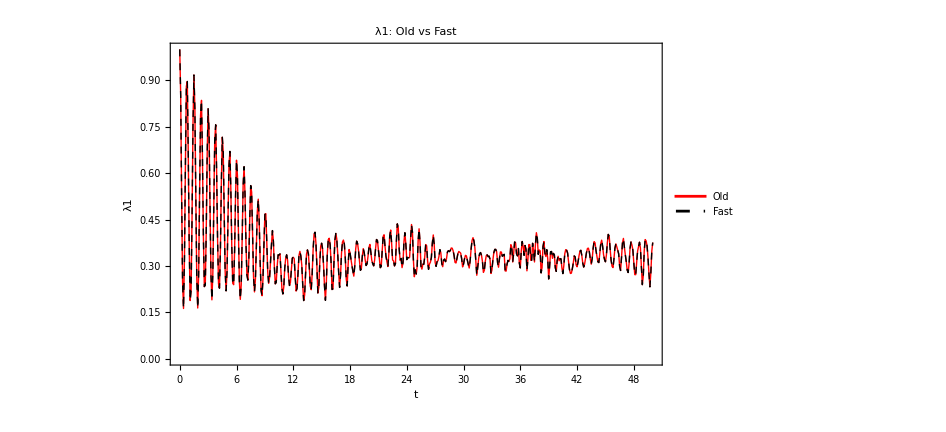
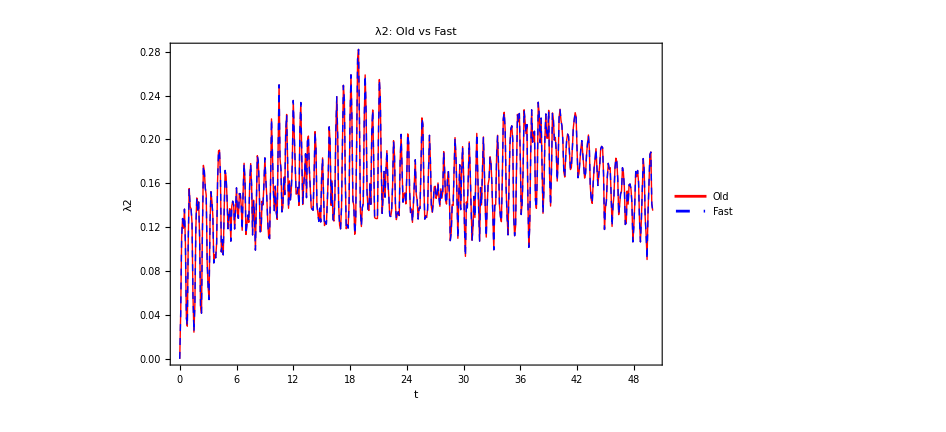
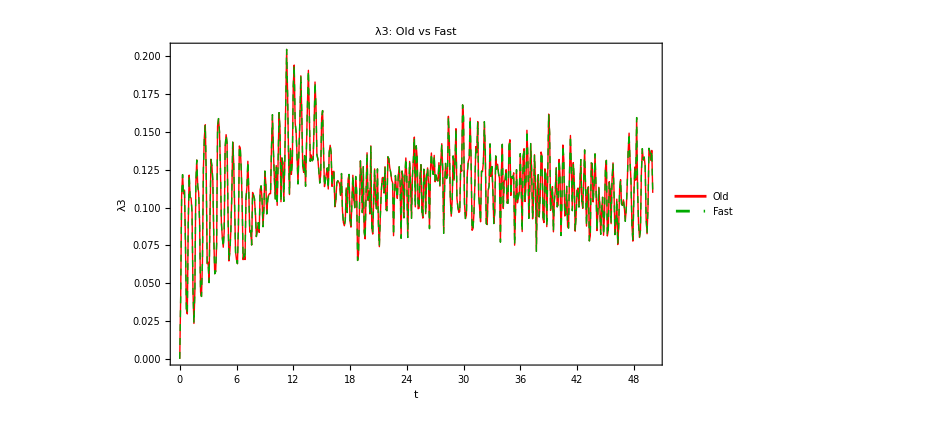
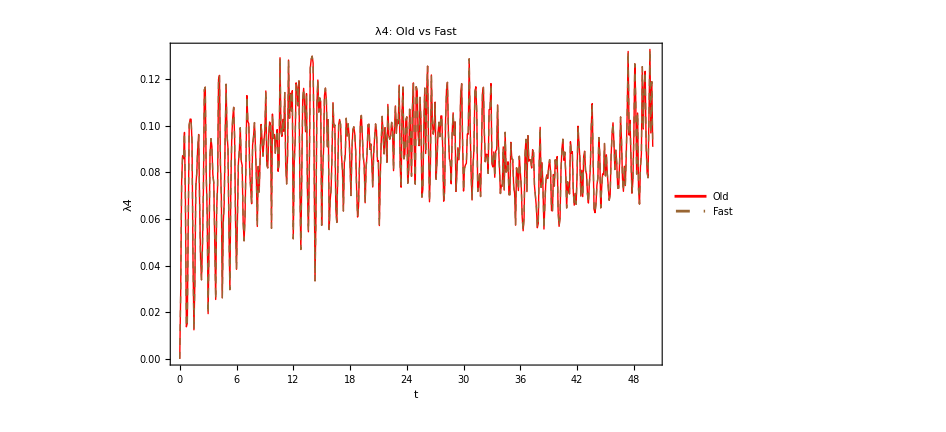

```mathematica
Table[Show[eigPanel[k],ImageSize->700], {k, 1, 4}]
```

## Export

```mathematica
runTag = "choiCompare_L" <> ToString[L] <> "_D" <> ToString[delta] <> "_beta" <> ToString[beta];
```

```mathematica
Export["combined_results_" <> runTag <> ".mx", combinedResults];
Export["side_by_side_" <> runTag <> ".png", sideBySidePanels, ImageResolution -> 200];
```

```mathematica
Print["Choi method comparison complete."];
Print["Max |ΔPurity| = ", maxDiffPurity,
      "   Max |ΔVNEntropy| = ", maxDiffVNEntropy,
      "   Max |Δλ_k| = ", eigMaxDiffs];
```

Choi method comparison complete.

Max |ΔPurity| = 2.7478×10^-15   Max |ΔVNEntropy| = 1.37668×10^-14   Max |Δλ_k| = {4.05231×10^-15,3.52496×10^-15,3.35842×10^-15,2.94209×10^-15}